# ELLIPSES

## Q16.What is an ellipse?

An ellipse is a closed curve similar to a circle.However, the radius
varies between a minimum diameter and a maximum diameter.In effect, an ellipse can be considered to be a squashed or stretched
circle.An axis - aligned ellipse can be specified as a centre (x_0, y_0) and
axis radii (a, b)

These can be combined to give the equation :

```mathematica
(x-x0)^2/a^2+(y-y0)^2/b^2 -1==0
```

-1+(x-x0)^2/a^2+(y-y0)^2/b^2==0

Expnding out this expression will generate an equation identical to that
of a circle.However, the values of A and B are not guaranteed to be
equal to one.The algebraic expression is :

```mathematica
{Axx,Axy,Ayy,Ax,Ay,A0}.{x^2,x y, y^2,x,y,1}==0
```

A0+Ax x+Axx x^2+Ay y+Axy x y+Ayy y^2==0

where {Axx,Axy,Ayy,Ax,Ay,A0} are constant terms.

## Q17.How do I calculate the Y coordinate if only the X coordinate is known?

Given the equation :

[1] Ax + By + Cx + Dy + Exy + F = 0

Then the known value of x or y is defined as : [2]

x = X

y = Y

Substituting[2] into[1] gives : 2 2

[3] AX + By + CX + Dy + EXy + F = 0

2 2
Ax + BY + Cx + DY + ExY + F = 0

Moving all constant terms to the end of the equation gives : 2 2

[4] By + Dy + EXy + AX + CX + F = 0

2 2
Ax + Cx + ExY + BY + DY + F = 0

Converting these into quadratic equations gives : 2 2

Ry + Sy + T = 0 Rx + Sx + T = 0

where : R = B R = A

S = D + Ey S = C + EY

2 2
T = AX + CX + F T = BY + DY + F

These values can be solved using quadratic equations.

## Q18.How do I determine the gradient of a point on a ellipse?

```mathematica
The equation of the ellipse is : 2 2
Ax + By + Cx + Dy + Exy + F = 0

The values of dx and dy are calculated from : dx = 2 Ax + C + Ey

dy = 2 By + D + Ex

The gradient is calculated from : dy 2 By + D + Ex
M = -- = ------------dx 2 Ax + C + Ey
```

## Q19.How do I determine the outward normal of a point on the ellipse?

```mathematica
The equation of the ellipse is : 2 2
Ax + By + Cx + Dy + Exy + F = 0

The values of dx and dy are calculated from : dx = 2 Ax + C + Ey

dy = 2 By + D + Ex

The outward normal is calculated from : N = (dy, -dx)
```

## Q20.How do I calculate the coefficients of an axis - aligned ellipse?

```mathematica
The algebraic exprssion of an ellipse is : 2 2
Ax + By + Cx + Dy + Exy + F = 0

where A, B, C, D, E and F are constant terms.Multiplying out the denominators in[1] gives : 2 2 2 2 2 2
s (x - c) + r (y - d) - r s = 0

Multiplying out the numerators in[1] gives : 2 2 2 2 2 2 2 2
s (x - 2 cx + c) + r (y - 2 dy + d) - r s = 0

Converting into single terms produces : 2 2 2 2 2 2 2 2 2 2 2 2
s x - s 2 cx + s c + r y - r 2 dy + r d - r s = 0

Multiplying every parameter by the denominator gives : 2 2 2 2 2 2 2 2 2 2 2 2
s x - s 2 cx + s c + r y - r 2 dy + r d - r s = 0

Rearranging into the algebraic expression gives : 2 2 2 2 2 2 2 2 2 2 2 2
s x + r y - s 2 cx - r 2 dy + r d + s c - r s = 0

The values of the constant terms are then as follows : 2
A = s

2
B = r

2
C = -s 2 c

2
D = -r 2 d


E = 0

2 2 2 2 2 2
F = r d + s c - r s

For an axis - aligned ellipse, A and B are always positive.For an axis - aligned ellipse, E is always zero, and F is always negative.These constants can be used to render the ellipse using an incremental
scan - line algorithm.
```

## Q21.How do I calculate the coefficients of an arbitary rotated ellipse?

The parameters calculated previously are only correct for an ellipse
which is aligned with the X and Y axii.The ellipse still has to be rotated by the desired angle.This is done
as follows : Rotating a pair of X and Y coordinates can be performed by the following
expression :

```mathematica
Row[{MatrixForm[RotationMatrix[θ]]," . ",MatrixForm[{x,y}]," = ",RotationMatrix[θ].{x,y}}]
```

(Cos[θ] | -Sin[θ]
Sin[θ] | Cos[θ]) . (x
y) = {x Cos[θ]-y Sin[θ],y Cos[θ]+x Sin[θ]}

Substituting the resulting matrix elements into equation[1] gives : 2 2

```mathematica
-1+((y-y0) Cos[θ]+(x-x0)  Sin[θ])^2/b^2+((x-x0) Cos[θ]-(y-y0) Sin[θ])^2/a^2==0
```

```mathematica
(x)^2/a^2+(y)^2/b^2 -1==0/.{x->x Cos[θ]-y Sin[θ],y->y Cos[θ]+x Sin[θ]}
out1=%/.{x->(x-x0),y->(y-y0)}
```

-1+(y Cos[θ]+x Sin[θ])^2/b^2+(x Cos[θ]-y Sin[θ])^2/a^2==0

-1+((y-y0) Cos[θ]+(x-x0) Sin[θ])^2/b^2+((x-x0) Cos[θ]-(y-y0) Sin[θ])^2/a^2==0

Multiplying out the denominators gives : 
Multiplying out the equations within the parenthesis gives :
Then rearranging into the order required by equation[2] gives :

```mathematica
Expand[a^2 b^2 (out1[[1]])];
out2=Collect[%,{x,y}]==0
```

-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2+x^2 (b^2 Cos[θ]^2+a^2 Sin[θ]^2)+y^2 (a^2 Cos[θ]^2+b^2 Sin[θ]^2)+y (-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2)+x (-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2+y (2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ]))==0

```mathematica
{{A0,Ay,Ayy},{Ax,Axy,Axyy},{Axx,Axxy,Axxyy}}=CoefficientList[out2[[1]],{x,y}];
Row[{MatrixForm[{{"A0","Ay","Ayy"},{"Ax","Axy","Axyy"},{"Axx","Axxy","Axxyy"}}]," = ",MatrixForm[{{A0,Ay,Ayy},{Ax,Axy,Axyy},{Axx,Axxy,Axxyy}}]}]
```

(A0 | Ay | Ayy
Ax | Axy | Axyy
Axx | Axxy | Axxyy) = (-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2 | -2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2 | a^2 Cos[θ]^2+b^2 Sin[θ]^2
-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2 | 2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ] | 0
b^2 Cos[θ]^2+a^2 Sin[θ]^2 | 0 | 0)

The values of the constant terms are then as follows :

```mathematica
Row[{MatrixForm[{"Axx","Axy","Ayy","Ax","Ay","A0"}]," = ",MatrixForm[{Axx,Axy,Ayy,Ax,Ay,A0}]}]
```

(Axx
Axy
Ayy
Ax
Ay
A0) = (b^2 Cos[θ]^2+a^2 Sin[θ]^2
2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ]
a^2 Cos[θ]^2+b^2 Sin[θ]^2
-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2
-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2
-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2)

```mathematica
TableForm[Map[(Row[{#[[1]]<>"=",#[[2]],";"}])&,Transpose[{{"Axx","Axy","Ayy","Ax","Ay","A0"},{Axx,Axy,Ayy,Ax,Ay,A0}}]]]
```

Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2;
Axy=2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ];
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2;
Ax=-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2;
Ay=-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2;
A0=-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2;

```mathematica
Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2;
Axy=2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ];
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2;
Ax=-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2;
Ay=-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2;
A0=-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2;
```

These values tend to get quite large, so 64 - bit integers will be
required.

```mathematica
Clear[EllipseCoeffsFromProperties]
EllipseCoeffsFromProperties[{{x0_,y0_},{a_,b_},θ_}]:=Module[{Axx,Axy,Ayy,Ax,Ay,A0},
Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2;
Axy=2 a^2 Cos[θ] Sin[θ]-2 b^2 Cos[θ] Sin[θ];
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2;
Ax=-2 b^2 x0 Cos[θ]^2-2 a^2 y0 Cos[θ] Sin[θ]+2 b^2 y0 Cos[θ] Sin[θ]-2 a^2 x0 Sin[θ]^2;
Ay=-2 a^2 y0 Cos[θ]^2-2 a^2 x0 Cos[θ] Sin[θ]+2 b^2 x0 Cos[θ] Sin[θ]-2 b^2 y0 Sin[θ]^2;
A0=-a^2 b^2+b^2 x0^2 Cos[θ]^2+a^2 y0^2 Cos[θ]^2+2 a^2 x0 y0 Cos[θ] Sin[θ]-2 b^2 x0 y0 Cos[θ] Sin[θ]+a^2 x0^2 Sin[θ]^2+b^2 y0^2 Sin[θ]^2;
{Axx,Axy,Ayy,Ax,Ay,A0}
]
```

```mathematica
Axx=b^2 Cos[θ]^2+a^2 Sin[θ]^2
Axy=-2 a^2 Cos[θ] Sin[θ]+2 b^2 Cos[θ] Sin[θ]
Ayy=a^2 Cos[θ]^2+b^2 Sin[θ]^2
Ax=-2 b^2 x0 Cos[θ]+2 a^2 y0 Sin[θ]
Ay=-2 a^2 y0 Cos[θ]-2 b^2 x0 Sin[θ]
A0=-a^2 b^2+b^2 x0^2+a^2 y0^2
```

-1225.+48.0527 x^2-9.34604 x y+25.9473 y^2==0

{7.91597×10^-25 (2.27511×10^23 x-2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2)),7.91597×10^-25 (2.27511×10^23 x+2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2))}

900-539.833 x+48.0527 x^2-196.672 y-9.34604 x y+25.9473 y^2==0

{9.39639×10^-37 (4.03329×10^36+1.91666×10^35 x-8.09121×10^8 √(-3.51589×10^55+3.83547×10^55 x-3.14777×10^54 x^2)),9.39639×10^-37 (4.03329×10^36+1.91666×10^35 x+8.09121×10^8 √(-3.51589×10^55+3.83547×10^55 x-3.14777×10^54 x^2))}

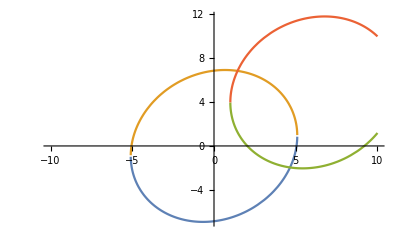

```mathematica
EllipseCoeffsFromProperties[{{0,0},{5,7},0.2}].{x^2,x y, y^2,x,y,1}==0
f1=y/.Solve[%,{x,y}]
EllipseCoeffsFromProperties[{{5,6},{5,7},0.2}].{x^2,x y, y^2,x,y,1}==0
f2=y/.Solve[%,{x,y}]
Plot[{f1,f2},{x,-10,10}]
```

```mathematica
Solve[%,{x,y}]
```

{{y→7.91597×10^-25 (-2.27511×10^23 x-2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2))},{y→7.91597×10^-25 (-2.27511×10^23 x+2.85107×10^7 √(9.26874×10^34-3.57214×10^33 x^2))}}

### Q22.How do I determine the limits for a rotated ellipse?

The equation of the ellipse is :

```mathematica
f={Axx,Axy,Ayy,Ax,Ay,A0}.{x^2,x y, y^2,x,y,1}==0
```

A0+Ax x+Axx x^2+Ay y+Axy x y+Ayy y^2==0

The derivative for the X - axis is :

```mathematica
D[f,x]
```

Ax+2 Axx x+Axy y==0

```mathematica
dx=Ax+2 Axx x+Axy y
```

The derivative for the Y - axis is :

```mathematica
D[f,x]
```

Ax+2 Axx x+Axy y==0

```mathematica
dy=Ax+2 Axx x+Axy y
```

When dx is zero, then the current location is at the left or right limit
of the ellipse.When dy is zero, then the current location is at the bottom or top limit
of the ellipse.Calculating the limits for Y gives : General equation of the circle :

```mathematica
f
```

A0+Ax x+Axx x^2+Ay y+Axy x y+Ayy y^2==0

Expressing y in terms of x gives :

```mathematica
Solve[D[f,x],y]
Solve[D[f,y],y]
```

{{y→(-Ax-2 Axx x)/Axy}}

{{y→(-Ay-Axy x)/(2 Ayy)}}

Substituting into equation[1] gives :

```mathematica
Collect[f/.Solve[D[f,x],y][[1]],x]
Collect[f/.Solve[D[f,y],y][[1]],x]
```

A0-(Ax Ay)/Axy+(Ax^2 Ayy)/Axy^2+(-(2 Axx Ay)/Axy+(4 Ax Axx Ayy)/Axy^2) x+(-Axx+(4 Axx^2 Ayy)/Axy^2) x^2==0

A0-Ay^2/(4 Ayy)+(Ax-(Axy Ay)/(2 Ayy)) x+(Axx-Axy^2/(4 Ayy)) x^2==0

```mathematica
Ax+By+Cx+Dy+Exy+F=0

[2] dx=2Ax+C+Ey

[3] dy=2By+D+Ex

2 2
[1] Ax+By+Cx+Dy+Exy+F=0

Derivative of Y:[2] 2By+D+Ex=0


2By=-Ex-D

-Ex-D
y=------2B

Substituting into equation[1] gives:2
2|-Ex-D|               |-Ex-D|      |-Ex-D|Ax+B|------- |+Cx+D|------- |+Ex|------- |+F=0
            |2B|               |2B|      |2B|Multiplying out last two brackets gives:2 2 2
2|(-Ex-D)(-Ex-D)|-DEx-D-E x-DEx
Ax+B|--------------   |+Cx+---------+-----------+F=0
            |2|2B 2B
4B

Expanding out all brackets produces:2 2 2 2 2
2|E x+2DEx+D|2DE 2D 2E 2 2DE
Ax+B|---------------- |+Cx----x-------x----x+F=0
            |2|4B 4B 4B 4B
4B

Cancelling out terms in first bracket and breaking up last two brackets:2 2 2 2 2
2 E x+2DEx+D 2DE 2D 2E 2 2DE
Ax+-----------------+Cx----x--------x----x+F=0
4B 4B 4B 4B 4B

Breaking up first bracket produces:2 2 2 2
2 E 2 2DE D 2DE 2D 2E 2 2DE
Ax+--x+---x+--+Cx----x--------x----x+F=0
4B 4B 4B 4B 4B 4B 4B

Some rearrangement produces:2 2 2 2
2 E 2 2E 2 2DE 2DE 2DE D 2D
Ax+--x----x+Cx+---x----x----x+------+F=0
4B 4B 4B 4B 4B 4B 4B

Cancelling out and combining some terms produces:2 2 2 2
2 E 2 2E 2 2DE-4DE D-2D
Ax+--x---x+Cx+---------x+--------+F=0
4B 4B 4B 4B

Further reduction produces:2 2 2
2 E-2E 2 2DE D
Ax+--------x+Cx----x---+F=0
4B 4B 4B

Final cancellation out produces:2 2
2-E 2 DE D
Ax+---x+Cx---x---+F=0
4B 2B 4B

Expressing as a quadratic equation with parameter t produces:2
Pt+Qt+R=0


The final equation for the Y-axis:
|2|      |        |     |2|
|E|2|DE|     |D|
|A--- |t+ |C--- |t+ |F--- | =0
     |4B|      |2A|     |4B|And for the X-axis:
|2|      |        |     |2|
|E|2|CE|     |C|
|B--- |t+ |D--- |t+ |F--- | =0
     |4A|      |2B|     |4A|This produces terms:Y-axis X-axis

        |2|         |2|
|E|         |E|P= |A--- |P= |B--- |
|4B|         |4A|
|        |         |        |
|DE|         |CE|Q= |C--- |Q= |D--- |
|2A|         |2B|
|2|         |2|
|D|         |C|R= |F--- |R= |F--- |
|4B|         |4A|Multiplying out by the common denominator produces:The terms for both the X-axis and Y-axis are as follows:X-axis Y-axis
----------------------------------2 2
P=4AB-E P=4AB-E


Q=4BC-2DE Q=4AD-2CE

2 2
R=4BF-D R=4AF-C

----------------------------------
```

```mathematica
Map[FullSimplify,Map[(ArcTan[#[[1]],#[[2]]])&,ellipseBoundingPoints[{{x0,y0},{a,b},θ}]]]
```

{ArcTan[x0+((a-b) (a+b) Sin[θ])/(√(b^2+a^2 Tan[θ]^2)),y0+Cos[θ] √(b^2+a^2 Tan[θ]^2)],ArcTan[x0+((-a+b) (a+b) Sin[θ])/(√(b^2+a^2 Tan[θ]^2)),y0-Cos[θ] √(b^2+a^2 Tan[θ]^2)],ArcTan[x0-Cos[θ] √(a^2+b^2 Tan[θ]^2),y0+((-a^2+b^2) Sin[θ])/(√(a^2+b^2 Tan[θ]^2))],ArcTan[x0+Cos[θ] √(a^2+b^2 Tan[θ]^2),y0+((a-b) (a+b) Sin[θ])/(√(a^2+b^2 Tan[θ]^2))]}

```mathematica
If[OddQ[Quotient[θ,Pi/2]],
  aa=b;bb=a,
  aa=a;bb=b]
```

```mathematica
Piecewise[{{a,0≤ θ<Pi/2},{b,Pi/2≤ θ<Pi},{a,Pi≤ θ<3Pi/2},{b,3Pi/2≤ θ<2Pi}}]
```

Piecewise[{{a, 0≤θ<π/2}, {b, π/2≤θ<π}, {a, π≤θ<(3 π)/2}, {b, (3 π)/2≤θ<2 π}, {0, True}}]

```mathematica
Grid[{{"θ -> ","δθ"},
{"a -> ","a"},
{"b -> ","b"}}]
```

θ ->  | δθ
a ->  | a
b ->  | b

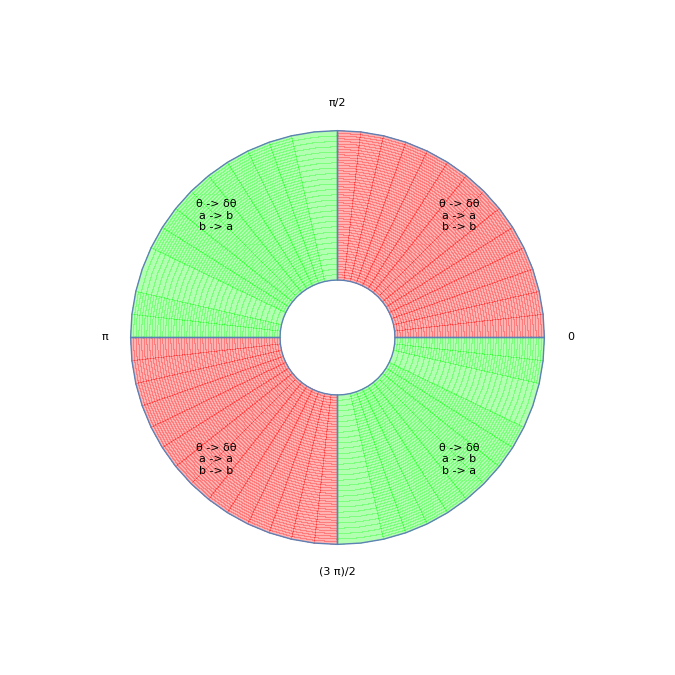

```mathematica
partShow[Piecewise[{{
Grid[{{"θ -> δθ"},{"a -> a"},{"b -> b"}}],0≤ θ<Pi/2||Pi≤ θ<3Pi/2},
{Grid[{{"θ -> δθ"},{"a -> b"},{"b -> a"}}],Pi/2≤ θ<Pi||3Pi/2≤ θ<2Pi}}]]
```

```mathematica
piecew
```

```mathematica
Block[{θ=0.2,x0=2,y0=3,a=3,b=2,aa,bb,at,bt,gfxSz=500},
If[OddQ[Quotient[θ,Pi/2]],
  aa=b;bb=a;at="b";bt="a";,
  aa=a;bb=b;at="a";bt="b";];
Θ=Quotient[θ,Pi/2]Pi/2;
δθ=Mod[θ,Pi/2];
Column[{
ellipseBoundingPoints[{{x0,y0},{aa,bb},δθ}],
ellipseBoundingBox[{{x0,y0},{aa,bb},δθ}]
}]
]
```

{{2.47519,5.04874},{1.52481,0.951257},{-0.966926,2.67187},{4.96693,3.32813}}
{{-1,5},{0,6}}

```mathematica
Manipulate[EllipticalBoundsFig=Block[{x0=2,y0=3,a=30,b=20,aa,bb,at,bt,gfxSz=500},
If[OddQ[Quotient[θ,Pi/2]],
  aa=b;bb=a;at="b";bt="a";,
  aa=a;bb=b;at="a";bt="b";];
Θ=Quotient[θ,Pi/2]Pi/2;
δθ=Mod[θ,Pi/2];
bBox=ellipseBoundingBox[{{x0,y0},{aa,bb},δθ}];
imgSz=ImageDimensions[Graphics[{EdgeForm[Red],FaceForm[None],Rectangle[Sequence@@Transpose[bBox]]},ImageSize->gfxSz]];
imgPltRng=Map[Abs[(#[[2]]-#[[1]])]&,plotRange[Graphics[{EdgeForm[Red],FaceForm[None],Rectangle[Sequence@@Transpose[bBox]]},ImageSize->gfxSz]]];
ebp=ellipseBoundingPoints[{{x0,y0},{aa,bb},δθ}];
tebp=Map[(11({x0,y0} - #)/12+{x0,y0})&,ebp];
Column[{
Graphics[{
{Dashed,Line[{{x0,y0}-bb{Cos[δθ+Pi/2],Sin[δθ+Pi/2]},{x0,y0}+bb{Cos[δθ+Pi/2],Sin[δθ+Pi/2]}}],Line[{{x0,y0}-aa{Cos[δθ],Sin[δθ]},{x0,y0}+aa{Cos[δθ],Sin[δθ]}}]},
{Black,PointSize[Large],Point[{x0,y0}],
  Text["(x0,y0)",{x0+0.1,y0-0.1},{-1,1},Background->White],
  Text["b",{x0+0.1,y0}+bb/2{Cos[δθ+Pi/2],Sin[δθ+Pi/2]},{-1,-1}],
  Text["a",{x0,y0}-aa/2 {Cos[δθ],Sin[δθ]},{-1,1}]},
{EdgeForm[Black],FaceForm[None],ellipse[{{x0,y0},{aa,bb},δθ}]},
{EdgeForm[Red],FaceForm[None],Rectangle[Sequence@@Transpose[bBox]]},
{Orange,PointSize[Large],Point[ebp],Table[{Text[Subscript[E, i],tebp[[i]]]},{i,1,4}]},
If[δθ>0,angleSymbol[{x0,y0},"δθ",{0,δθ},Green,imgSz,imgPltRng]]},ImageSize->gfxSz],
Row[{"θ = ",Θ," + ",δθ}],
Row[{"θ -> ",δθ}],
Row[{"a -> ",at}],
Row[{"b -> ",bt}]
}]
],{{θ,0.2},-2 Pi, 2 Pi}]
```

```mathematica
Export[figPath<>"Elliptical_Bounds"<>".jpg",EllipticalBoundsFig,ImageResolution->300,ImageFormattingWidth->Infinity]
```

/Users/jaspershemilt/Developer/projects/Color-Space-WriteUp/WriteUp/Dissertation/Chapter4/Figs/Elliptical_Bounds.jpg

```mathematica
ellipseBoundingPoints[{{x0,y0},{a,b},θ}]
```

{{x0+((a-b) (a+b) Sin[θ])/(√(b^2+a^2 Tan[θ]^2)),y0+Cos[θ] √(b^2+a^2 Tan[θ]^2)},{x0-((a-b) (a+b) Sin[θ])/(√(b^2+a^2 Tan[θ]^2)),y0-Cos[θ] √(b^2+a^2 Tan[θ]^2)},{x0-Cos[θ] √(a^2+b^2 Tan[θ]^2),y0-((a-b) (a+b) Sin[θ])/(√(a^2+b^2 Tan[θ]^2))},{x0+Cos[θ] √(a^2+b^2 Tan[θ]^2),y0+((a-b) (a+b) Sin[θ])/(√(a^2+b^2 Tan[θ]^2))}}

```mathematica
ellipseBoundingBox[{{{x0_,y0_},{a_,b_},θ_}}]
```

```mathematica
Reduce[√(1+(b^2 Cot[θ]^2)/a^2)==1/a √(a^2+b^2 Cot[θ]^2)]
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==(-√(Power[«2»]+Times[«2»])-a √(Power[«2»] Plus[«2»]))/a,0==-√(a^2+Power[«2»] Power[«2»])+a √((Power[«2»]+Times[«2»])/a^2),0==(√(a^2+Power[«2»] Power[«2»])-a √(Power[«2»] Plus[«2»]))/a,0==-√(a^2+Power[«2»] Power[«2»])+a √((Power[«2»]+Times[«2»])/a^2)}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

(a≠0&&0==(-√(a^2+b^2 Cot[θ]^2)-a √((a^2+b^2 Cot[θ]^2)/a^2))/a&&0==-√(a^2+b^2 Cot[θ]^2)+a √((a^2+b^2 Cot[θ]^2)/a^2))||(a≠0&&0==(√(a^2+b^2 Cot[θ]^2)-a √((a^2+b^2 Cot[θ]^2)/a^2))/a&&0==-√(a^2+b^2 Cot[θ]^2)+a √((a^2+b^2 Cot[θ]^2)/a^2))

```mathematica
Manipulate[Block[{Θ,δθ},
Θ=Quotient[θ,Pi/2]Pi/2; δθ=Mod[θ,Pi/2];
Row[{"θ = ",Θ," + ",δθ}]
],{{θ,0.2},-2 Pi,2Pi}]
```

```mathematica
Θ=Quotient[θ,Pi/2]Pi/2
δθ=Mod[θ,Pi/2]
```